# Prepare

```mathematica
imgsize=800;
SetDirectory@NotebookDirectory[];
```

```mathematica
Get["../../neupackage/mma/neutrino.wl"]
```

```mathematica
Get["../../neupackage/mma/neumat.wl"]
```

```mathematica
colorpalette5={RGBColor[172,151,62],
RGBColor[129,118,204],
RGBColor[91,169,102],
RGBColor[199,90,147],
RGBColor[204,95,67]}
```

{RGBColor[172,151,62],RGBColor[129,118,204],RGBColor[91,169,102],RGBColor[199,90,147],RGBColor[204,95,67]}

```mathematica
markers=Graphics`PlotMarkers[]
```

{{●,8.96},{■,8.96},{◆,10.88},{▲,10.24},{▼,10.24},{○,10.24},{□,10.24},{◇,10.24},{△,11.136},{▽,11.136}}

## Rabi Oscillation

```mathematica
ampRabi[a_,k_,omegam_]:=(Abs[a]^2/4)/(Abs[a]^2/4+(k-omegam)^2);
```

```mathematica
probRabi[a_,k_,omegam_,x_]:=(Abs[a]^2/4)/(Abs[a]^2/4+(k-omegam)^2)Sin[(√(Abs[a]^2/4+(k-omegam)^2))/2 x]^2;
```

```mathematica
ampRabi2[a_,k_,omegam_]:=Abs[a]^2/(Abs[a]^2+(k-omegam)^2);
```

```mathematica
probRabi2[a_,k_,omegam_,x_]:=Abs[a]^2/(Abs[a]^2+(k-omegam)^2)Sin[(√(Abs[a]^2+(k-omegam)^2))/2 x]^2;
```

## Resonance & Off-resonance

```mathematica
endpoint=1000000;

(*thetam=Pi/7;*)


thetaV=ArcSin[√0.093]/2
energy10 = 10;
deltamsquare13=2.6*10^(-15);(*MeV^2*)
deltamsquare13text="2.6*e-15";
omegaV=OmegaVacuum[energy10,deltamsquare13](*MeV*)
fraction=0.5;
lambda0=fraction*Cos[2thetaV]omegaV (*MeV*)
thetam=Mod[ArcTan[Sin[2thetaV]/(Cos[2thetaV]-(lambda0/omegaV)^2)]/2,Pi]


a1 =10^(-4);(*3.5* 10^(-5);*)
k1=1;
deltalambda[a_,k_,x_]:=a Sin[k x];
```

0.154948

1.3×10^-16

6.19038×10^-17

0.198931

```mathematica
dellam[x_]:=a1 Sin[k1 x];
dellam2[x_]:=a1 Cos[k1 x];
```

```mathematica
sys1=I D[{psi1[x],psi2[x]},x]==(-PauliMatrix[3]/2+dellam[x]Cos[2thetam]PauliMatrix[3]/2-dellam[x]Sin[2thetam]PauliMatrix[1]/2).{psi1[x],psi2[x]}&&{psi1[0],psi2[0]}=={1,0}
```

{ⅈ psi1'[x],ⅈ psi2'[x]}=={psi2[x] (0.-0.0000193725 Sin[x])+psi1[x] (-0.5+0.0000460946 Sin[x]),psi2[x] (0.5-0.0000460946 Sin[x])+psi1[x] (0.-0.0000193725 Sin[x])}&&{psi1[0],psi2[0]}=={1,0}

```mathematica
sol1=NDSolve[sys1,{psi1,psi2},{x,0,endpoint}]
```

$Aborted

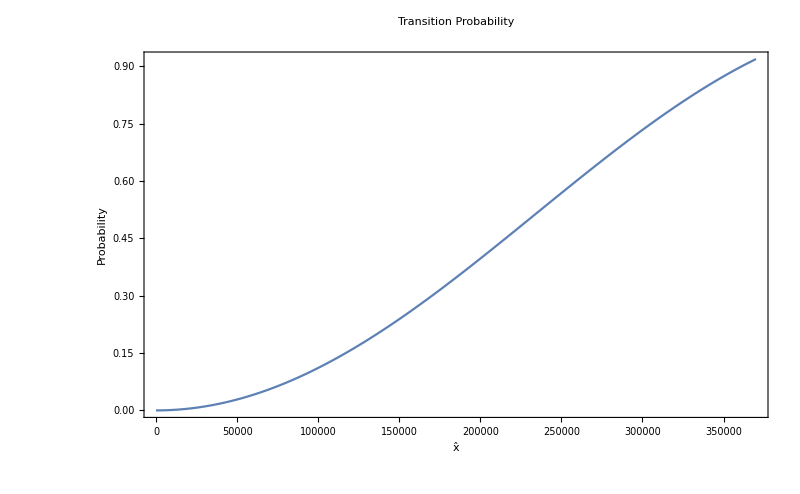

```mathematica
sol1List=Table[{x,Abs[psi2[x]]^2/.First@sol1},{x,0,endpoint/2.7,endpoint/1000}];
ListPlot[sol1List,Joined->True,Frame->True,ImageSize->imgsize,PlotLabel->"Transition Probability",FrameLabel->{"x̂","Probability"},LabelStyle->Black,FrameTicksStyle->Larger,BaseStyle->{FontSize->15},Epilog->Inset[Style["A_1="<>ToString@N[a1]<>"\n k_1=1",FontSize->14],{0,1},{Left,Top}]]
```

Remove the diagonal element of the perturbation

```mathematica
sys2=I D[{psi1[x],psi2[x]},x]==(-PauliMatrix[3]/2-dellam[x]Sin[2thetam]PauliMatrix[1]/2).{psi1[x],psi2[x]}&&{psi1[0],psi2[0]}=={1,0}
sol2=NDSolve[sys2,{psi1,psi2},{x,0,endpoint}]
```

{ⅈ psi1'[x],ⅈ psi2'[x]}=={-0.5 psi1[x]-6.78036×10^-6 psi2[x] Sin[x],0.5 psi2[x]-6.78036×10^-6 psi1[x] Sin[x]}&&{psi1[0],psi2[0]}=={1,0}

{{psi1→                                 6
InterpolatingFunction[{{0., 1. 10 }}, <>],psi2→                                 6
InterpolatingFunction[{{0., 1. 10 }}, <>]}}

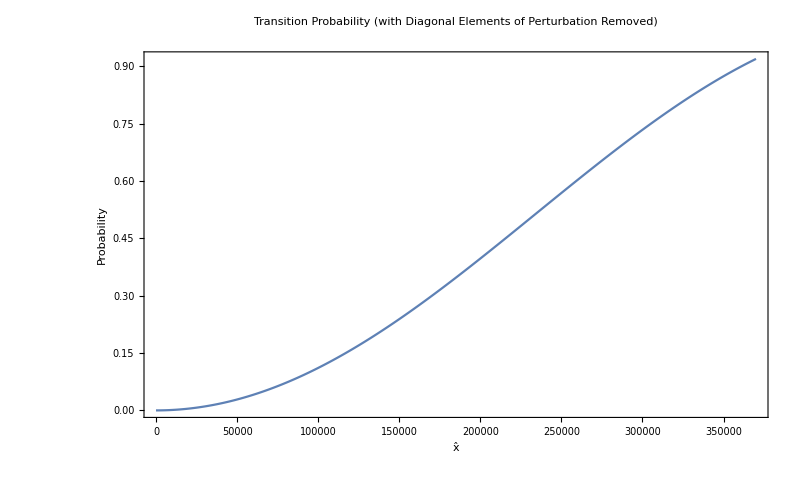

```mathematica
sol2List=Table[{x,Abs[psi2[x]]^2/.First@sol2},{x,0,endpoint/2.7,endpoint/1000}];
ListPlot[sol2List,Joined->True,Frame->True,ImageSize->imgsize,PlotLabel->"Transition Probability (with Diagonal Elements of Perturbation Removed)",FrameLabel->{"x̂","Probability"},LabelStyle->Black,FrameTicksStyle->Larger,BaseStyle->{FontSize->15},Epilog->Inset[Style["A_1="<>ToString@N[a1]<>"\n k_1=1",FontSize->14],{0,1},{Left,Top}]]
```

Combine the two results and compare

```mathematica
ListPlot[{sol1List,sol2List},Joined->True,PlotStyle->{Black,{Orange,Dashed}},Frame->True,ImageSize->imgsize,PlotLabel->"Transition Probability",FrameLabel->{"x̂","Probability"},LabelStyle->Black,FrameTicksStyle->Larger,BaseStyle->{FontSize->15},Epilog->Inset[Style["A_1="<>ToString@N[a1]<>"\n k_1=1",FontSize->14],{0,1},{Left,Top}],PlotLegends->Placed[{"Origianl System","with Diagonal Elements of Perturbation Removed"},{Center,Above}]]
```

-Graphics-

Adding in a slow rotating field (a new perturbation)

```mathematica
a2=10^(-2);
k2=0.1;
dellamSlow[x_]:=a2 Sin[k2 x];
```

```mathematica
sys3=I D[{psi1[x],psi2[x]},x]==(-PauliMatrix[3]/2+(dellam[x]+dellamSlow[x])Cos[2thetam]PauliMatrix[3]/2-(dellam[x]+dellamSlow[x])Sin[2thetam]PauliMatrix[1]/2).{psi1[x],psi2[x]}&&{psi1[0],psi2[0]}=={1,0}

sol3=NDSolve[sys3,{psi1,psi2},{x,0,endpoint}]
```

{ⅈ psi1'[x],ⅈ psi2'[x]}=={psi2[x] (0.-0.193725 (1/100 Sin[0.1 x]+0.000035 Sin[x]))+psi1[x] (-0.5+0.460946 (1/100 Sin[0.1 x]+0.000035 Sin[x])),psi2[x] (0.5-0.460946 (1/100 Sin[0.1 x]+0.000035 Sin[x]))+psi1[x] (0.-0.193725 (1/100 Sin[0.1 x]+0.000035 Sin[x]))}&&{psi1[0],psi2[0]}=={1,0}

{{psi1→                                 6
InterpolatingFunction[{{0., 1. 10 }}, <>],psi2→                                 6
InterpolatingFunction[{{0., 1. 10 }}, <>]}}

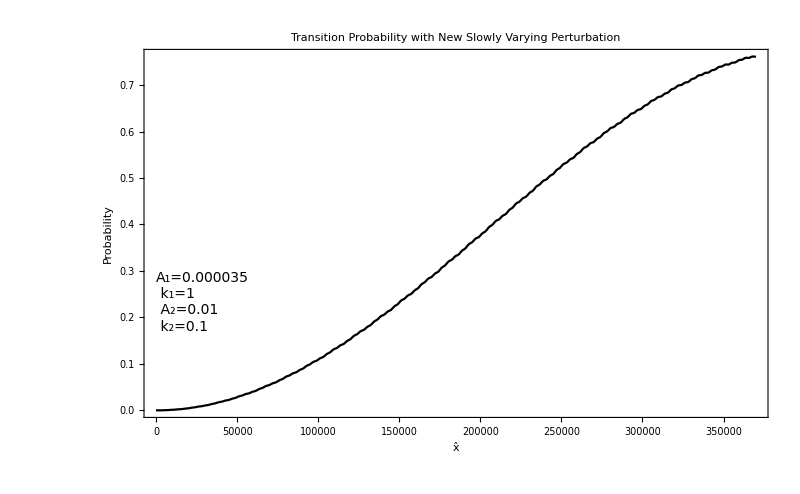

```mathematica
sol3List=Table[{x,Abs[psi2[x]]^2/.First@sol3},{x,0,endpoint/2.7,endpoint/1000}];
ListPlot[sol3List,Joined->True,PlotStyle->Black,Frame->True,ImageSize->imgsize,PlotLabel->"Transition Probability with New Slowly Varying Perturbation",FrameLabel->{"x̂","Probability"},LabelStyle->Black,FrameTicksStyle->Larger,BaseStyle->{FontSize->15},Epilog->Inset[Style["A_1="<>ToString@N[a1]<>"\n k_1="<>ToString@k1<>"\n A_2="<>ToString@N[a2]<>"\n k_2="<>ToString@k2,FontSize->14],{1,0.3},{Left,Top}]]
```

```mathematica
sys4=I D[{psi1[x],psi2[x]},x]==(-PauliMatrix[3]/2+(dellam[x])Cos[2thetam]PauliMatrix[3]/2-(dellam[x]+dellamSlow[x])Sin[2thetam]PauliMatrix[1]/2).{psi1[x],psi2[x]}&&{psi1[0],psi2[0]}=={1,0}

sol4=NDSolve[sys4,{psi1,psi2},{x,0,endpoint}]
```

{ⅈ psi1'[x],ⅈ psi2'[x]}=={psi2[x] (0.-0.193725 (1/100 Sin[0.1 x]+0.000035 Sin[x]))+psi1[x] (-0.5+0.0000161331 Sin[x]),psi1[x] (0.-0.193725 (1/100 Sin[0.1 x]+0.000035 Sin[x]))+psi2[x] (0.5-0.0000161331 Sin[x])}&&{psi1[0],psi2[0]}=={1,0}

{{psi1→                                 6
InterpolatingFunction[{{0., 1. 10 }}, <>],psi2→                                 6
InterpolatingFunction[{{0., 1. 10 }}, <>]}}

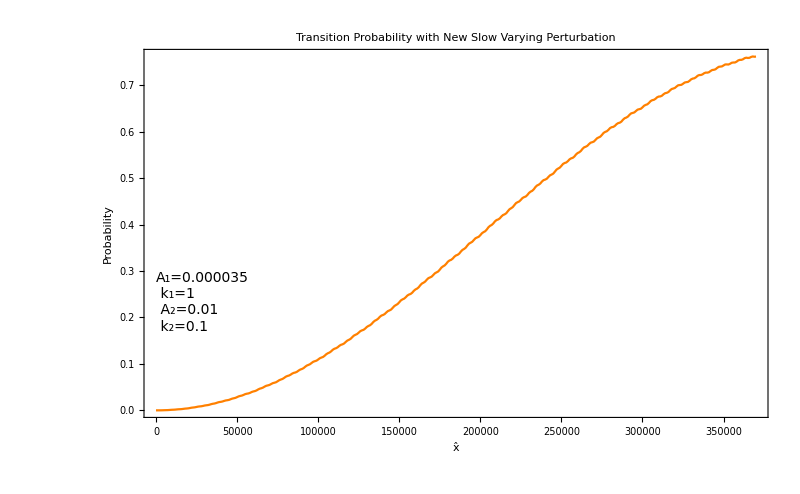

```mathematica
sol4List=Table[{x,Abs[psi2[x]]^2/.First@sol4},{x,0,endpoint/2.7,endpoint/1000}];
ListPlot[sol4List,Joined->True,PlotStyle->Orange,Frame->True,ImageSize->imgsize,PlotLabel->"Transition Probability with New Slow Varying Perturbation",FrameLabel->{"x̂","Probability"},LabelStyle->Black,FrameTicksStyle->Larger,BaseStyle->{FontSize->15},Epilog->Inset[Style["A_1="<>ToString@N[a1]<>"\n k_1="<>ToString@k1<>"\n A_2="<>ToString@N[a2]<>"\n k_2="<>ToString@k2,FontSize->14],{1,0.3},{Left,Top}]]
```

```mathematica
ListPlot[{sol3List,sol4List},Joined->True,PlotStyle->{Black,{Orange,Dashing[{0.03,0.03}]}},Frame->True,ImageSize->imgsize,PlotLabel->"Transition Probability with New Slowly Varying Perturbation",FrameLabel->{"x̂","Probability"},LabelStyle->Black,FrameTicksStyle->Larger,BaseStyle->{FontSize->15},Epilog->Inset[Style["A_1="<>ToString@N[a1]<>"\n k_1="<>ToString@k1<>"\n A_2="<>ToString@N[a2]<>"\n k_2="<>ToString@k2,FontSize->14],{1,0.3},{Left,Top}],PlotLegends->Placed[{"Original Result","Remove Diagonal Elements of Slow Perturbation"},{Center,Above}]]
```

-Graphics-

Shift out of resonance

```mathematica
a2prime=1*√(2*1*a1*Sin[2thetam])/Cos[2thetam]^2
k2prime =k2;
dellamSlowPrime=deltalambda[a2prime,k2prime,x]
```

0.0190304

0.0190304 Sin[0.1 x]

```mathematica
sys5=I D[{psi1[x],psi2[x]},x]==(-PauliMatrix[3]/2+(dellam[x]+dellamSlowPrime)Cos[2thetam]PauliMatrix[3]/2-(dellam[x]+dellamSlowPrime)Sin[2thetam]PauliMatrix[1]/2).{psi1[x],psi2[x]}&&{psi1[0],psi2[0]}=={1,0}
```

{ⅈ psi1'[x],ⅈ psi2'[x]}=={psi1[x] (-1/2+1/2 Sin[(3 π)/14] (0.0190304 Sin[0.1 x]+0.000035 Sin[x]))-1/2 Cos[(3 π)/14] psi2[x] (0.0190304 Sin[0.1 x]+0.000035 Sin[x]),psi2[x] (1/2-1/2 Sin[(3 π)/14] (0.0190304 Sin[0.1 x]+0.000035 Sin[x]))-1/2 Cos[(3 π)/14] psi1[x] (0.0190304 Sin[0.1 x]+0.000035 Sin[x])}&&{psi1[0],psi2[0]}=={1,0}

```mathematica
sol5=NDSolve[sys5,{psi1,psi2},{x,0,endpoint}]
```

{{psi1→                                 6
InterpolatingFunction[{{0., 1. 10 }}, <>],psi2→                                 6
InterpolatingFunction[{{0., 1. 10 }}, <>]}}

```mathematica
sol5List=Table[{x,Abs[psi2[x]]^2/.First@sol5},{x,0,endpoint/2.7,endpoint/1000}];
ListPlot[sol5List,Joined->True,PlotStyle->Orange,Frame->True,ImageSize->imgsize,PlotLabel->"Transition Probability with New Slow Rotating Perturbation",FrameLabel->{"x̂","Probability"},LabelStyle->Black,FrameTicksStyle->Larger,BaseStyle->{FontSize->15},Epilog->Inset[Style["A_1="<>ToString@N[a1]<>"\n k_1="<>ToString@k1<>"\n A_2="<>ToString@N[a2prime]<>"\n k_2="<>ToString@k2prime,FontSize->14],{-6000,0.06},{Left,Top}]]
```

```mathematica
a2prime2=10*√(2*1*a1*Sin[2thetam])/Cos[2thetam]^2
k2prime2=k2;
dellamSlowPrime2=deltalambda[a2prime2,k2prime2,x]
```

0.190304

0.190304 Sin[0.1 x]

```mathematica
sys6=I D[{psi1[x],psi2[x]},x]==(-PauliMatrix[3]/2+(dellam[x]+dellamSlowPrime2)Cos[2thetam]PauliMatrix[3]/2-(dellam[x]+dellamSlowPrime2)Sin[2thetam]PauliMatrix[1]/2).{psi1[x],psi2[x]}&&{psi1[0],psi2[0]}=={1,0}
```

{ⅈ psi1'[x],ⅈ psi2'[x]}=={psi1[x] (-1/2+1/2 Sin[(3 π)/14] (0.190304 Sin[0.1 x]+0.000035 Sin[x]))-1/2 Cos[(3 π)/14] psi2[x] (0.190304 Sin[0.1 x]+0.000035 Sin[x]),psi2[x] (1/2-1/2 Sin[(3 π)/14] (0.190304 Sin[0.1 x]+0.000035 Sin[x]))-1/2 Cos[(3 π)/14] psi1[x] (0.190304 Sin[0.1 x]+0.000035 Sin[x])}&&{psi1[0],psi2[0]}=={1,0}

```mathematica
sol6=NDSolve[sys6,{psi1,psi2},{x,0,endpoint}]
```

{{psi1→                                 6
InterpolatingFunction[{{0., 1. 10 }}, <>],psi2→                                 6
InterpolatingFunction[{{0., 1. 10 }}, <>]}}

```mathematica
sol6List=Table[{x,Abs[psi2[x]]^2/.First@sol6},{x,0,endpoint/2.7,endpoint/1000}];
```

```mathematica
sol6List2=Table[{x,Abs[psi2[x]]^2/.First@sol6},{x,0,endpoint,endpoint/1000}];
ListPlot[sol6List2,Joined->True,PlotStyle->Blue,Frame->True,ImageSize->imgsize,PlotLabel->"Transition Probability with New Slow Rotating Perturbation",FrameLabel->{"x̂","Probability"},LabelStyle->Black,FrameTicksStyle->Larger,BaseStyle->{FontSize->15},Epilog->Inset[Style["A_1="<>ToString@N[a1]<>"\n k_1="<>ToString@k1<>"\n A_2="<>ToString@N[a2prime]<>"\n k_2="<>ToString@k2prime,FontSize->14],{-6000,0.06},{Left,Top}]]
```

```mathematica
ListPlot[{sol4List,sol5List,sol6List},Joined->True,PlotStyle->{Black,Orange,Blue},Frame->True,ImageSize->imgsize,PlotLabel->"Transition Probability with New Slow Rotating Perturbation",FrameLabel->{"x̂","Probability"},LabelStyle->Black,FrameTicksStyle->Larger,BaseStyle->{FontSize->15},Epilog->Inset[Style["A_1="<>ToString@N[a1]<>"\n k_1="<>ToString@k1<>"\n k_2="<>ToString@k2prime,FontSize->14],{1000,0.4},{Left,Top}],PlotLegends->Placed[{"A_2="<>ToString@N@a2,"A_2="<>ToString@a2prime,"A_2="<>ToString@a2prime2},{Center,Above}],GridLines->{None,{{ampRabi[a1 Sin[2thetam],k1,√((a2 Sin[2thetam])^2+1)],Black},{ampRabi[a1 Sin[2thetam],k1,√((a2prime Sin[2thetam])^2+1)],Orange},{ampRabi[a1 Sin[2thetam],k1,√((a2prime2 Sin[2thetam])^2+1)],Orange}}}]
```

```mathematica
Abs[k1-√((a2 Sin[2thetam])^2+1)]/(a1 Sin[2thetam]) 
Abs[k1-√((a2prime Sin[2thetam])^2+1)]/(a1 Sin[2thetam])
Abs[k1-√((a2prime2 Sin[2thetam])^2+1)]/(a1 Sin[2thetam])
```

1.11689

4.04469

402.277

One simple question: 

Does the z component of the perturbation matter in this case?

```mathematica
ListPlot[{sol4List,sol5List,sol6List},Joined->True,PlotStyle->{Black,Orange,Blue},Frame->True,ImageSize->imgsize,PlotLabel->"Transition Probability with New Slow Rotating Perturbation",FrameLabel->{"x̂","Probability"},LabelStyle->Black,FrameTicksStyle->Larger,BaseStyle->{FontSize->15},Epilog->Inset[Style["A_1="<>ToString@N[a1]<>"\n k_1="<>ToString@k1<>"\n k_2="<>ToString@k2prime,FontSize->14],{1000,0.4},{Left,Top}],PlotLegends->Placed[{"A_2="<>ToString@N@a2,"A_2="<>ToString@a2prime,"A_2="<>ToString@a2prime2},{Center,Above}],GridLines->{None,{{ampRabi[a1 ,k1,√((a2 )^2+1)],Black},{ampRabi[a1 ,k1,√((a2prime )^2+1)],Orange},{ampRabi[a1 ,k1,√((a2prime2 )^2+1)],Orange}}}]
```

Theory

We are treating the second slow perturbation as a shift of energy gap, which means we could predict the wavelength etc

Rabi oscillation has a oscillatary transition probability predicted by the formula we provided in the beginning of this notebook.

```mathematica
theory1List=Table[{x,probRabi[a1 Sin[2thetam],k1,1,x]},{x,0,endpoint/2.7,endpoint/1000}];

theoryNumerical1=ListPlot[{theory1List,sol1List},Joined->True,Frame->True,PlotStyle->{Red,Black},ImageSize->imgsize,PlotLabel->"Transition Probability",FrameLabel->{"x̂","Probability"},LabelStyle->Black,FrameTicksStyle->Larger,BaseStyle->{FontSize->15},Epilog->Inset[Style["A_1="<>ToString@N[a1]<>"\n k_1=1",FontSize->14],{0,1},{Left,Top}],PlotLegends->Placed[{"Theory","Numerical"},{Center,Above}]]
```

Adding back the slow perturbation

```mathematica
theory3List=Table[{x,probRabi[a1 Sin[2thetam],k1,√((a2 Sin[2thetam])^2+1),x]},{x,0,endpoint/2.7,endpoint/1000}];

theoryNumerical2=ListPlot[{theory3List,sol3List},Joined->True,Frame->True,PlotStyle->{Red,Black},ImageSize->imgsize,PlotLabel->"Transition Probability with Slow Perturbation",FrameLabel->{"x̂","Probability"},LabelStyle->Black,FrameTicksStyle->Larger,BaseStyle->{FontSize->15},Epilog->Inset[Style["A_1="<>ToString@N[a1]<>"\n k_1=1"<>"\n A_2="<>ToString@N@a2<>"\n k_2="<>ToString@k2,FontSize->14],{0,0.4},{Left,Top}],PlotLegends->Placed[{"Theory","Numerical"},{Center,Above}]]
```

```mathematica
theoryNumerical12=Grid[{{theoryNumerical1},{theoryNumerical2}}]
```

Rotating Perturbation

```mathematica
sys7=I D[{psi1[x],psi2[x]},x]==(-PauliMatrix[3]/2+(dellam[x]+dellamSlow[x])Cos[2thetam]PauliMatrix[3]/2-(dellam[x]+dellamSlow[x])Sin[2thetam]PauliMatrix[1]/2+(dellamSlow[x])Sin[2thetam]PauliMatrix[2]/2).{psi1[x],psi2[x]}&&{psi1[0],psi2[0]}=={1,0};
sol7=NDSolve[sys7,{psi1,psi2},{x,0,endpoint}];
sol7List=Table[{x,Abs[psi2[x]]^2/.First@sol7},{x,0,endpoint/2.7,endpoint/1000}];
```

```mathematica
sys8=I D[{psi1[x],psi2[x]},x]==(-PauliMatrix[3]/2+(dellam[x]+dellamSlowPrime)Cos[2thetam]PauliMatrix[3]/2-(dellam[x]+dellamSlowPrime)Sin[2thetam]PauliMatrix[1]/2+(dellamSlowPrime) Sin[2thetam]PauliMatrix[2]/2).{psi1[x],psi2[x]}&&{psi1[0],psi2[0]}=={1,0};

sol8=NDSolve[sys8,{psi1,psi2},{x,0,endpoint}];

sol8List=Table[{x,Abs[psi2[x]]^2/.First@sol8},{x,0,endpoint/2.7,endpoint/1000}];
```

```mathematica
sys9=I D[{psi1[x],psi2[x]},x]==(-PauliMatrix[3]/2+(dellam[x]+dellamSlowPrime2)Cos[2thetam]PauliMatrix[3]/2-(dellam[x]+dellamSlowPrime2)Sin[2thetam]PauliMatrix[1]/2+(dellamSlowPrime2) Sin[2thetam]PauliMatrix[2]/2).{psi1[x],psi2[x]}&&{psi1[0],psi2[0]}=={1,0};

sol9=NDSolve[sys9,{psi1,psi2},{x,0,endpoint}];

sol9List=Table[{x,Abs[psi2[x]]^2/.First@sol9},{x,0,endpoint/2.7,endpoint/1000}];
```

Theories of these cases

```mathematica
theory7List=Table[{x,probRabi[a1 Sin[2thetam],k1,√((a2 Sin[2thetam])^2+1),x]},{x,0,endpoint/2.7,endpoint/1000}];
theory8List=Table[{x,probRabi[a1 Sin[2thetam],k1,√((a2prime Sin[2thetam])^2+1),x]},{x,0,endpoint/2.7,endpoint/1000}];
```

```mathematica
ListPlot[{sol7List,sol8List,theory7List,theory8List(*,sol10List,theory10List*)},Joined->True,PlotStyle->{Lighter@Black,Orange,{Black,Dotted},{Orange,Dotted}},Frame->True,ImageSize->imgsize,PlotLabel->"Transition Probability with Rotating Field",FrameLabel->{"x̂","Probability"},LabelStyle->Black,FrameTicksStyle->Larger,BaseStyle->{FontSize->15},Epilog->Inset[Style["A_1="<>ToString@N[a1]<>"\n k_1="<>ToString@k1<>"\n k_2="<>ToString@k2prime,FontSize->14],{1000,0.4},{Left,Top}],PlotLegends->Placed[{"A_2="<>ToString@N@a2,"A_2="<>ToString@a2prime,"Rabi Formula of A_2="<>ToString@N@a2,"Rabi Formula of A_2="<>ToString@a2prime},{Center,Above}]]
```

A not so perfect part

```mathematica
ListPlot[{sol7List,sol8List,sol9List,theory7List},Joined->True,PlotStyle->{Black,Orange,Blue,{Lighter@Black,Dashing[{0.02,0.02}]}},Frame->True,ImageSize->imgsize,PlotLabel->"Transition Probability with Rotating Field",FrameLabel->{"x̂","Probability"},LabelStyle->Black,FrameTicksStyle->Larger,BaseStyle->{FontSize->15},Epilog->Inset[Style["A_1="<>ToString@N[a1]<>"\n k_1="<>ToString@k1<>"\n k_2="<>ToString@k2prime,FontSize->14],{1000,0.4},{Left,Top}],PlotLegends->Placed[{"A_2="<>ToString@N@a2,"A_2="<>ToString@a2prime,"A_2="<>ToString@a2prime2},{Center,Above}],GridLines->{None,{{ampRabi[a1 Sin[2thetam],k1,√((a2 Sin[2thetam])^2+1)],Black},{ampRabi[a1 Sin[2thetam],k1,√((a2prime Sin[2thetam])^2+1)],Orange},{ampRabi[a1 Sin[2thetam],k1,√((a2prime2 Sin[2thetam])^2+1)],Blue}}}]
```

Demonstrate Pure Rabi

We can chose amplitude of a2 according to the desired Q

```mathematica
a2FromQ[q_,a1_]:=√(2a1 q)

a2FromQ[0.001,a1]
a2FromQ[1,a1]
a2FromQ[3,a1]
```

0.000447214

1/(50 √2)

(√(3/2))/50

```mathematica
k2P=0.01
```

0.01

```mathematica
a2Critical=N@√(2(a1+k1-1))
a2PureRabi=N@{a2FromQ[0.001,a1],a2FromQ[3,a1]}(*a2PureRabi=N@{10*a1,0.015}*) (*N@{a2*2,a2*3}*)
```

0.0141421

{0.000447214,0.0244949}

```mathematica
dellamPureRabiSin[x_]:=a2 Sin[k2P x];
dellamPureRabiCos[x_]:=a2 Cos[k2P x];
dellamSin[x_]:=a1 Sin[k1 x];
dellamCos[x_]:=a1 Cos[k1 x];
dellamPureRabi1Sin[x_]:=a2PureRabi[[1]] Sin[k2P x]
dellamPureRabi1Cos[x_]:=a2PureRabi[[1]] Cos[k2P x]
dellamPureRabi2Sin[x_]:=a2PureRabi[[2]] Sin[k2P x]
dellamPureRabi2Cos[x_]:=a2PureRabi[[2]] Cos[k2P x]
(*dellamPureRabi3Sin[x_]:=a2PureRabi[[3]] Sin[k2P x]
dellamPureRabi3Cos[x_]:=a2PureRabi[[3]] Cos[k2P x]
*)
dellamSlowCriticalSin[x_]:=a2Critical Sin[k2P x]
dellamSlowCriticalCos[x_]:=a2Critical Cos[k2P x]

dellamCoordSin[x_]:=a1 Sin[k1 x]/Sin[2thetam]*2;
dellamCoordCos[x_]:=a1 Cos[k1 x]/Sin[2thetam]*2;
```

The one perturbation case

```mathematica
sys10=I D[{psi1[x],psi2[x]},x]==(-PauliMatrix[3]/2-(dellamCos[x])PauliMatrix[1]/2+(dellamSin[x])PauliMatrix[2]/2).{psi1[x],psi2[x]}&&{psi1[0],psi2[0]}=={1,0};

sol10=NDSolve[sys10,{psi1,psi2},{x,0,endpoint},AccuracyGoal->20];
sol10List =Table[{x,Abs[psi2[x]]^2/.First@sol10},{x,0,endpoint/2.7,endpoint/1000}];
```

```mathematica
sys10P=I D[{psi1[x],psi2[x]},x]==(-PauliMatrix[3]/2+(dellamCoordSin[x])Cos[2thetam]PauliMatrix[3]/2-(dellamCoordSin[x])Sin[2thetam]PauliMatrix[1]/2).{psi1[x],psi2[x]}&&{psi1[0],psi2[0]}=={1,0};

sol10P=NDSolve[sys10P,{psi1,psi2},{x,0,endpoint},AccuracyGoal->20];
sol10PList =Table[{x,Abs[psi2[x]]^2/.First@sol10P},{x,0,endpoint/2.7,endpoint/1000}];
```

```mathematica
sys11=I D[{psi1[x],psi2[x]},x]==(-PauliMatrix[3]/2-(dellamCos[x]+dellamPureRabiCos[x])PauliMatrix[1]/2+(dellamSin[x]+dellamPureRabiSin[x])PauliMatrix[2]/2).{psi1[x],psi2[x]}&&{psi1[0],psi2[0]}=={1,0};


sol11=NDSolve[sys11,{psi1,psi2},{x,0,endpoint}];

sol11List=Table[{x,Abs[psi2[x]]^2/.First@sol11},{x,0,endpoint/2.7,endpoint/1000}];
```

```mathematica
sys12=I D[{psi1[x],psi2[x]},x]==(-PauliMatrix[3]/2-(dellamCos[x]+dellamPureRabi1Cos[x])PauliMatrix[1]/2+(dellamSin[x]+dellamPureRabi1Sin[x]) PauliMatrix[2]/2).{psi1[x],psi2[x]}&&{psi1[0],psi2[0]}=={1,0};

sol12=NDSolve[sys12,{psi1,psi2},{x,0,endpoint}];

sol12List=Table[{x,Abs[psi2[x]]^2/.First@sol12},{x,0,endpoint,endpoint/1000}];
```

```mathematica
(*sys13=I D[{psi1[x],psi2[x]},x]==(-PauliMatrix[3]/2-(dellamCos[x]+dellamSlowPrime2Cos[x])PauliMatrix[1]/2+(dellamSin[x]+dellamSlowPrime2Sin[x]) PauliMatrix[2]/2).{psi1[x],psi2[x]}&&{psi1[0],psi2[0]}=={1,0};

sol13=NDSolve[sys13,{psi1,psi2},{x,0,endpoint}];

sol13List=Table[{x,Abs[psi2[x]]^2/.First@sol13},{x,0,endpoint/2.7,endpoint/1000}];*)
```

```mathematica
sys14=I D[{psi1[x],psi2[x]},x]==(-PauliMatrix[3]/2-(dellamCos[x]+dellamPureRabi2Cos[x])PauliMatrix[1]/2+(dellamSin[x]+dellamPureRabi2Sin[x]) PauliMatrix[2]/2).{psi1[x],psi2[x]}&&{psi1[0],psi2[0]}=={1,0};

sol14=NDSolve[sys14,{psi1,psi2},{x,0,endpoint}];

sol14List=Table[{x,Abs[psi2[x]]^2/.First@sol14},{x,0,endpoint,endpoint/1000}];
```

```mathematica
sys15Critical=I D[{psi1[x],psi2[x]},x]==(-PauliMatrix[3]/2-(dellamCos[x]+dellamSlowCriticalCos[x])PauliMatrix[1]/2+(dellamSin[x]+dellamSlowCriticalSin[x]) PauliMatrix[2]/2).{psi1[x],psi2[x]}&&{psi1[0],psi2[0]}=={1,0};

sol15Critical=NDSolve[sys15Critical,{psi1,psi2},{x,0,endpoint}];

sol15CriticalList=Table[{x,Abs[psi2[x]]^2/.First@sol15Critical},{x,0,endpoint,endpoint/1000}];
```

```mathematica
theory10List=Table[{x,probRabi2[a1,k1,1,x]},{x,0,endpoint,endpoint/1000}];
theory10Amp=ampRabi2[a1,k1,1];
theory11List=Table[{x,probRabi2[a1,k1,√((a2 )^2+1),x]},{x,0,endpoint,endpoint/1000}];
theory11Amp=ampRabi2[a1,k1,√((a2 )^2+1)];
theory12List=Table[{x,probRabi2[a1,k1,√((a2PureRabi[[1]] )^2+1),x]},{x,0,endpoint,endpoint/1000}];
theory12Amp=ampRabi2[a1,k1,√((a2PureRabi[[1]] )^2+1)];
(*theory13List=Table[{x,probRabi2[a1,k1,√((a2prime2 )^2+1),x]},{x,0,endpoint/2.7,endpoint/1000}];*)
theory14List=Table[{x,probRabi2[a1,k1,√((a2PureRabi[[2]] )^2+1),x]},{x,0,endpoint,endpoint/1000}];
theory14Amp=ampRabi2[a1,k1,√((a2PureRabi[[2]] )^2+1)];
theory15CriticalList=Table[{x,probRabi2[a1,k1,√((a2Critical )^2+1),x]},{x,0,endpoint,endpoint/1000}];
theory15CriticalAmp=ampRabi2[a1,k1,√((a2Critical )^2+1)];
```

```mathematica
(*Export["../../ipynb/papers/assets/rabi-oscillations-energy-gap-change/resonance.csv",sol10List]
Export["../../ipynb/papers/assets/rabi-oscillations-energy-gap-change/a2Critical.csv",sol15CriticalList]
Export["../../ipynb/papers/assets/rabi-oscillations-energy-gap-change/a2-0.01.csv",sol11List]
Export["../../ipynb/papers/assets/rabi-oscillations-energy-gap-change/a2-0.02.csv",sol12List]
Export["../../ipynb/papers/assets/rabi-oscillations-energy-gap-change/a2-0.03.csv",sol14List]*)

(*Export["../../ipynb/papers/assets/rabi-oscillations-energy-gap-change/resonance-k2-0-01.csv",sol10List]
Export["../../ipynb/papers/assets/rabi-oscillations-energy-gap-change/a2Critical-k2-0-01.csv",sol15CriticalList]
Export["../../ipynb/papers/assets/rabi-oscillations-energy-gap-change/a2-0.01-k2-0-01.csv",sol11List]
Export["../../ipynb/papers/assets/rabi-oscillations-energy-gap-change/a2-0.02-k2-0-01.csv",sol12List]
Export["../../ipynb/papers/assets/rabi-oscillations-energy-gap-change/a2-0.03-k2-0-01.csv",sol14List]*)

(*Export["../../ipynb/papers/assets/rabi-oscillations-energy-gap-change/a2-list.csv",N@Join[{a2Critical},{a2},a2PureRabi]]*)
(*Export["../../ipynb/papers/assets/rabi-oscillations-energy-gap-change/a2-list-k2-0-01.csv",N@Join[{a2Critical},{a2},a2PureRabi]]*)
```

```mathematica
rabiOscillationsEnergyGapChange=ListPlot[{sol14List,sol15CriticalList,sol12List,sol12List},Joined->True,PlotStyle->{Directive[Black,Dashed],Directive[Darker@Green,Dashing[{0.015,0.015}]],Directive[Blue,Dotted],Red},Frame->True,ImageSize->imgsize*1.5,PlotLabel->"Transition Probability with Different Perturbations",FrameLabel->{"x̂","Probability"},LabelStyle->Black,FrameTicksStyle->Larger,BaseStyle->{FontSize->15},Epilog->Inset[Style["A_1="<>ToString@N[a1]<>"\n k_1="<>ToString@k1<>"\n k_2="<>ToString@k2P,FontSize->14],{1000,0.8},{Left,Top}],PlotLegends->Placed[{"A_2="<>ToString@0,"A_2="<>ToString@N@a2Critical,"A_2="<>ToString@N@a2,"A_2="<>ToString@a2PureRabi[[1]],"A_2="<>ToString@N@a2PureRabi[[2]]},{Center,Above}],PlotRange->Full,GridLines->{None, {{theory10Amp,Directive[Black,Thick,Dashed]},{theory11Amp,Directive[Blue,Thick,Dotted]},{theory12Amp,Directive[Red,Thick]},{theory15CriticalAmp,Directive[Darker@Green,Thick,Dashing[{0.015,0.015}]]}}}]
```

-Graphics-

```mathematica
(*Export["../../ipynb/papers/assets/rabi-oscillations-energy-gap-change/rabi-oscillations-energy-gap-change.pdf",rabiOscillationsEnergyGapChange]
Export["../../ipynb/papers/assets/rabi-oscillations-energy-gap-change/rabi-oscillations-energy-gap-change.eps",rabiOscillationsEnergyGapChange]
Export["../../ipynb/papers/assets/rabi-oscillations-energy-gap-change/rabi-oscillations-energy-gap-change.png",rabiOscillationsEnergyGapChange]*)
```

```mathematica
markers
```

{{●,8.96},{■,8.96},{◆,10.88},{▲,10.24},{▼,10.24},{○,10.24},{□,10.24},{◇,10.24},{△,11.136},{▽,11.136}}

Export data to csv for use of python

```mathematica
(*Export["../../ipynb/papers/assets/rabi-oscillations-energy-gap-change/interference/sol10List-a1-"<>ToString[a1]<>"-k1-"<>ToString[k1]<>".csv",sol10List]
Export["../../ipynb/papers/assets/rabi-oscillations-energy-gap-change/interference/theory10List-a1-"<>ToString[a1]<>"-k1-"<>ToString[k1]<>".csv",theory10List]
*)
Export["../../ipynb/papers/assets/rabi-oscillations-energy-gap-change/interference/sol15List-a2-"<>ToString[a2Critical]<>"-k2-"<>ToString[k2P]<>".csv",sol15CriticalList]
Export["../../ipynb/papers/assets/rabi-oscillations-energy-gap-change/interference/theory15List-a2-"<>ToString[a2Critical]<>"-k2-"<>ToString[k2P]<>".csv",theory15CriticalList]

(*Export["../../ipynb/papers/assets/rabi-oscillations-energy-gap-change/interference/sol11List-a1-a2-"<>ToString[a1]<>"-"<>ToString[N@a2]<>"-k1-k2-"<>ToString[k1]<>"-"<>ToString[k2P]<>".csv",sol11List]
Export["../../ipynb/papers/assets/rabi-oscillations-energy-gap-change/interference/theory11List-a1-a2-"<>ToString[a1]<>"-"<>ToString[N@a2]<>"-k1-k2-"<>ToString[k1]<>"-"<>ToString[k2P]<>".csv",theory11List]
*)
Export["../../ipynb/papers/assets/rabi-oscillations-energy-gap-change/interference/sol12List-a1-a2-"<>ToString[N@a1]<>"-"<>ToString[N@a2PureRabi[[1]]]<>"-k1-k2-"<>ToString[k1]<>"-"<>ToString[k2P]<>".csv",sol12List]
Export["../../ipynb/papers/assets/rabi-oscillations-energy-gap-change/interference/theory12List-a1-a2-"<>ToString[N@a1]<>"-"<>ToString[N@a2PureRabi[[1]]]<>"-k1-k2-"<>ToString[k1]<>"-"<>ToString[k2P]<>".csv",theory12List]

Export["../../ipynb/papers/assets/rabi-oscillations-energy-gap-change/interference/sol14List-a1-a2-"<>ToString[N@a1]<>"-"<>ToString[N@a2PureRabi[[2]]]<>"-k1-k2-"<>ToString[k1]<>"-"<>ToString[k2P]<>".csv",sol14List]
Export["../../ipynb/papers/assets/rabi-oscillations-energy-gap-change/interference/theory14List-a1-a2-"<>ToString[N@a1]<>"-"<>ToString[N@a2PureRabi[[2]]]<>"-k1-k2-"<>ToString[k1]<>"-"<>ToString[k2P]<>".csv",theory14List]
```

../../ipynb/papers/assets/rabi-oscillations-energy-gap-change/interference/sol15List-a2-0.0141421-k2-0.01.csv

../../ipynb/papers/assets/rabi-oscillations-energy-gap-change/interference/theory15List-a2-0.0141421-k2-0.01.csv

../../ipynb/papers/assets/rabi-oscillations-energy-gap-change/interference/sol12List-a1-a2-0.0001-0.000447214-k1-k2-1-0.01.csv

../../ipynb/papers/assets/rabi-oscillations-energy-gap-change/interference/theory12List-a1-a2-0.0001-0.000447214-k1-k2-1-0.01.csv

../../ipynb/papers/assets/rabi-oscillations-energy-gap-change/interference/sol14List-a1-a2-0.0001-0.0244949-k1-k2-1-0.01.csv

../../ipynb/papers/assets/rabi-oscillations-energy-gap-change/interference/theory14List-a1-a2-0.0001-0.0244949-k1-k2-1-0.01.csv

```mathematica
rabiOscillationsEnergyGapChange01=ListPlot[{sol10List[[1;;;;5]],sol15CriticalList[[1;;;;5]],sol11List[[1;;;;5]],sol12List[[1;;;;5]],theory10List,theory15CriticalList,theory11List,theory12List,sol10PList[[1;;;;4]]},Joined->{False,False,False,False,True,True,True,True,False},PlotMarkers->{{"○",11},{"□",13},{"◇",13},{"△",13},""," ","  ","   ",{"+",18},{"○",11.136}},PlotStyle->{Black,Darker@Darker@Darker@Green,Blue,Red,Directive[Black,Dashed],Directive[Darker@Darker@Darker@Green,DotDashed],Directive[Blue,Dotted],Red},Frame->True,ImageSize->imgsize*1.1,PlotLabel->"Transition Probability with Rotating Field",FrameLabel->{"ω_mx","Probability"},LabelStyle->Black,FrameTicksStyle->Larger,BaseStyle->{FontSize->14},Epilog->Inset[Style["A_1="<>ToString@N[a1]<>"\n k_1="<>ToString@k1<>"\n k_2="<>ToString@k2P,FontSize->14],{1000,0.8},{Left,Top}],PlotLegends->Placed[{"A_2="<>ToString@0,"A_2="<>ToString@a2Critical,"A_2="<>ToString@a2PureRabi[[1]],"A_2="<>ToString@a2PureRabi[[2]],"Rabi Formula for A_2="<>ToString@N@0,"Rabi Formula for A_2="<>ToString@a2Critical,"Rabi Formula for A_2="<>ToString@a2PureRabi[[1]],"Rabi Formula for A_2="<>ToString@a2PureRabi[[2]],"Neutrino Oscillations with Matter Perturbation"},Below],PlotRange->Full,ImagePadding->{{Automatic, 10}, {Automatic, 10}}]
```

-Graphics-

```mathematica
(*Export["../../ipynb/papers/assets/rabi-oscillations-energy-gap-change/rabi-oscillations-energy-gap-change-k2-0-01.pdf",rabiOscillationsEnergyGapChange01]
Export["../../ipynb/papers/assets/rabi-oscillations-energy-gap-change/rabi-oscillations-energy-gap-change-k2-0-01.eps",rabiOscillationsEnergyGapChange01]
Export["../../ipynb/papers/assets/rabi-oscillations-energy-gap-change/rabi-oscillations-energy-gap-change-k2-0-01.png",rabiOscillationsEnergyGapChange01]*)
```

```mathematica
rabiOscillationsNeutrinoCoincidence=ListPlot[{sol10List[[1;;;;5]],theory10List,sol10PList[[1;;;;4]]},Joined->{False,True,False},PlotMarkers->{{"○",11},"",{"+",18},{"○",11.136}},PlotStyle->{Black,Directive[Black,Dashed],Red},Frame->True,ImageSize->imgsize*1.1,PlotLabel->"Transition Probability for Rabi Oscillation and Neutrino Transition",FrameLabel->{"ω_mx","Probability"},LabelStyle->Black,FrameTicksStyle->Larger,BaseStyle->{FontSize->14},Epilog->Inset[Style["A_R="<>ToString@N[a1]<>"\n k_R="<>ToString@k1<>"\n E="<>ToString@energy10<>" MeV\n θ_v="<>ToString@thetaV<>"\n Δm^2="<>deltamsquare13text<>"\n λ_0="<>ToString@fraction<>"λ_MSW",FontSize->14],{1000,0.8},{Left,Top}],PlotLegends->Placed[{"Rabi Oscillation","Rabi Formula","Neutrino Oscillations with Matter Perturbation"},Below],PlotRange->Full,ImagePadding->{{Automatic, 10}, {Automatic, 10}}]
```

-Graphics-

```mathematica
(*Export["../../ipynb/papers/assets/rabi-oscillations-energy-gap-change/rabiOscillationsNeutrinoCoincidence.pdf",rabiOscillationsNeutrinoCoincidence]*)
```

Export the data for python plotting

```mathematica
NotebookDirectory[]
```

/Users/leima/GitHub/NeuPhysics/codebase/mma/matter/

```mathematica
Export["../../../../rabi-neutrino-oscillations/data/theory10List.csv",Transpose@theory10List]
Export["../../../../rabi-neutrino-oscillations/data/sol10PList.csv",Transpose@sol10PList]
```

../../../../rabi-neutrino-oscillations/data/theory10List.csv

../../../../rabi-neutrino-oscillations/data/sol10PList.csv

Modes

First of all check if only the first mode is good enough for single frequency matter profile on resonance.

```mathematica
sys10Original=I D[{psi1[x],psi2[x]},x]==(-PauliMatrix[3]/2-(a1 Sin[k1 x])PauliMatrix[1]+(a1 Cot[2thetam]Sin[k1 x])PauliMatrix[3]).{psi1[x],psi2[x]}&&{psi1[0],psi2[0]}=={1,0};

sol10Original=NDSolve[sys10Original,{psi1,psi2},{x,0,endpoint},AccuracyGoal->20];
sol10OriginalList =Table[{x,Abs[psi2[x]]^2/.First@sol10Original},{x,0,endpoint/2.7,endpoint/1000}];
```

```mathematica
?qValueOrderdList
```

gives ordered list of qValues and also their corresponding integer combinations; Example, qValueOrderdList[listNGenerator[6,3],kNListTest,aNListTest,phiNListTest,thetamTest]

```mathematica
qValueList=Part[qValueOrderdList[listNGenerator[1,4],{k1},{a1},{0},thetam],1;;5];
Grid@%
```

{1} | 0.
{-1} | 294970.
{2} | 9.14176×10^9
{-2} | 2.74253×10^10
{3} | 2.26658×10^15

```mathematica
sys10Modes=I D[{psi1[x],psi2[x]},x]==(-PauliMatrix[3]/2-(Tan[2thetam]k1 BesselJ[1,2a1 Cot[2thetam]/k1]Cos[k1 x])PauliMatrix[1]/2+(Tan[2thetam]k1 BesselJ[1,2a1 Cot[2thetam]/k1]Sin[k1 x])PauliMatrix[2]/2).{psi1[x],psi2[x]}&&{psi1[0],psi2[0]}=={1,0};

sol10Modes=NDSolve[sys10Modes,{psi1,psi2},{x,0,endpoint},AccuracyGoal->20];
sol10ModesList =Table[{x,Abs[psi2[x]]^2/.First@sol10Modes},{x,0,endpoint/2.7,endpoint/1000}];
```

```mathematica
ListPlot[{sol10List[[1;;;;5]],theory10List,sol10PList[[1;;;;4]],sol10ModesList[[1;;;;4]],sol10OriginalList[[1;;;;7]]},Joined->{False,True,False,False,False},PlotMarkers->{{"○",11},"",{"+",18},{"○",11},{"+",18}},PlotStyle->{Black,Directive[Black,Dashed],Red,Blue},Frame->True,ImageSize->imgsize*1.1,PlotLabel->"Transition Probability for Rabi Oscillation and Neutrino Transition",FrameLabel->{"ω_mx","Probability"},LabelStyle->Black,FrameTicksStyle->Larger,BaseStyle->{FontSize->14},Epilog->Inset[Style["A_R="<>ToString@N[a1]<>"\n k_R="<>ToString@k1<>"\n E="<>ToString@energy10<>" MeV\n θ_v="<>ToString@thetaV<>"\n Δm^2="<>deltamsquare13text<>"\n λ_0="<>ToString@fraction<>"λ_MSW",FontSize->14],{1000,0.8},{Left,Top}],PlotLegends->Placed[{"Rabi Oscillation","Rabi Formula","Neutrino Oscillations with Matter Perturbation"},Below],PlotRange->Full,ImagePadding->{{Automatic, 10}, {Automatic, 10}}]
```

-Graphics-

F**k why? If they are the same we should have the same detuning and width (for the resonance wavelength)

```mathematica
Tan[2thetam]k1 BesselJ[1,2a1 Cot[2thetam]/k1]
Tan[2thetam]
k1
BesselJ[1,2a1 Cot[2thetam]/k1]
2a1 Cot[2thetam]/k1
a1
```

0.000035

0.420276

1

0.0000832785

0.000166557

0.000035

```mathematica
Series[BesselJ[1,z],{z,0,2}]
```

z/2+O[z]^3

For more complicated cases

```mathematica
mprobRabi[a_,k_,omegam_,x_]:=Abs[a]^2/(Abs[a]^2+(k-omegam)^2)Sin[(√(Abs[a]^2+(k-omegam)^2))/2 x]^2;
```

```mathematica
qValueList=Part[qValueOrderdList[listNGenerator[2,20],{k1,k2},{a1,a2},{0,0},thetam],1;;100];
Grid@%
```

{-1,20} | 0.
{0,10} | 0.
{1,0} | 0.
{2,-10} | 0.
{3,-20} | 0.
{0,1} | 465.071
{0,-1} | 568.42
{0,2} | 8965.27
{0,-2} | 13447.9
{1,1} | 291183.
{-1,0} | 295597.
{0,3} | 340310.
{1,-1} | 355891.
{0,-3} | 632005.
{-1,-1} | 6.11485×10^6
{-1,1} | 6.76192×10^6
{0,4} | 1.89825×10^7
{1,2} | 2.31544×10^7
{1,-2} | 3.47317×10^7
{0,-4} | 4.42925×10^7
{-1,-2} | 2.54699×10^8
{-1,2} | 3.12585×10^8
{0,5} | 1.37262×10^9
{1,3} | 2.08621×10^9
{1,-3} | 3.87439×10^9
{0,-5} | 4.11787×10^9
{2,0} | 9.16121×10^9
{-1,-3} | 1.59943×10^10
{-1,3} | 2.19549×10^10
{-2,0} | 2.74836×10^10
{0,6} | 1.19108×10^11
{2,-1} | 1.88088×10^11
{2,1} | 2.07991×10^11
{1,4} | 2.24118×10^11
{0,-6} | 4.76431×10^11
{1,-4} | 5.22942×10^11
{-2,-1} | 5.86157×10^11
{-2,1} | 6.0606×10^11
{-1,-4} | 1.34471×10^12
{-1,4} | 2.09177×10^12
{2,-2} | 7.65448×10^12
{2,2} | 9.39413×10^12
{0,7} | 1.16275×10^13
{-2,-2} | 2.5051×10^13
{-2,2} | 2.67907×10^13
{1,5} | 2.83604×10^13
{0,-7} | 6.58892×10^13
{1,-5} | 8.50813×10^13
{-1,-5} | 1.41802×10^14
{-1,5} | 2.55244×10^14
{2,-3} | 4.61468×10^14
{2,3} | 6.33444×10^14
{0,8} | 1.17715×10^15
{-2,-3} | 1.60797×10^15
{-2,3} | 1.77995×10^15
{3,0} | 2.27141×10^15
{1,6} | 4.15284×10^15
{-3,0} | 4.54282×10^15
{0,-8} | 1.05943×10^16
{1,-6} | 1.66114×10^16
{-1,-6} | 1.79956×10^16
{2,-4} | 3.6466×10^16
{-1,6} | 3.87598×10^16
{3,-1} | 4.83761×10^16
{3,1} | 5.00187×10^16
{2,4} | 5.67249×10^16
{-3,-1} | 9.76556×10^16
{-3,1} | 9.92983×10^16
{0,9} | 1.02148×10^17
{-2,-4} | 1.3776×10^17
{-2,4} | 1.58019×10^17
{1,7} | 6.9246×10^17
{0,-9} | 1.94082×10^18
{3,-2} | 2.05881×10^18
{3,2} | 2.20178×10^18
{-1,-7} | 2.67092×10^18
{2,-5} | 3.51581×10^18
{1,-7} | 3.92394×10^18
{-3,-2} | 4.2034×10^18
{-3,2} | 4.34637×10^18
{2,5} | 6.32846×10^18
{-1,7} | 7.28732×10^18
{-2,-5} | 1.47664×10^19
{-2,5} | 1.7579×10^19
{1,8} | 1.29715×10^20
{3,-3} | 1.31214×10^20
{3,3} | 1.45248×10^20
{-3,-3} | 2.71551×10^20
{-3,3} | 2.85584×10^20
{2,-6} | 3.92246×10^20
{0,-10} | 3.98883×10^20
{-1,-8} | 4.54003×10^20
{4,0} | 6.33563×10^20
{2,6} | 8.44837×10^20
{-4,0} | 1.05594×10^21
{1,-8} | 1.16744×10^21
{-1,8} | 1.75115×10^21
{-2,-6} | 1.90088×10^21
{-2,6} | 2.35347×10^21
{0,11} | 4.32672×10^21

```mathematica
mb1=widthNList[{1,0},{k1,k2},{a1,a2},{0,0},thetam]
mb2=widthNList[{0,1},{k1,k2},{a1,a2},{0,0},thetam]
mk1={1,0}.{k1,k2}
mk2={0,1}.{k1,k2}
```

0.0000136688

0.00390726

1.

0.1

```mathematica
msys1=I D[{psi1[x],psi2[x]},x]==(-PauliMatrix[3]/2-(mb1 Cos[mk1 x])PauliMatrix[1]/2+(mb1 Sin[mk1 x])PauliMatrix[2]/2).{psi1[x],psi2[x]}&&{psi1[0],psi2[0]}=={1,0}

msol1=NDSolve[msys1,{psi1,psi2},{x,0,endpoint}]
```

{ⅈ psi1'[x],ⅈ psi2'[x]}=={-0.5 psi1[x]+psi2[x] (-6.83438×10^-6 Cos[1. x]-(0.+6.83438×10^-6 ⅈ) Sin[1. x]),0.5 psi2[x]+psi1[x] (-6.83438×10^-6 Cos[1. x]+(0.+6.83438×10^-6 ⅈ) Sin[1. x])}&&{psi1[0],psi2[0]}=={1,0}

{{psi1→                                 6
InterpolatingFunction[{{0., 1. 10 }}, <>],psi2→                                 6
InterpolatingFunction[{{0., 1. 10 }}, <>]}}

```mathematica
msol1List=Table[{x,Abs[psi2[x]]^2/.First@msol1},{x,0,endpoint/2.7,endpoint/1000}];
```

```mathematica
ListPlot[msol1List,Joined->True,PlotStyle->Black,Frame->True,ImageSize->imgsize,PlotLabel->"Transition Probability",FrameLabel->{"x̂","Probability"},LabelStyle->Black,FrameTicksStyle->Larger,BaseStyle->{FontSize->15},Epilog->Inset[Style["B_1="<>ToString@N[mb1]<>"\n ϕ_1="<>ToString[mk1],FontSize->14],{0,1},{Left,Top}]]
```

We can predict what is the require B2 to destroy the resonance (slow rotating modes): B2 Critical value

```mathematica
mb2C=√(2mb1)
```

0.00522853

```mathematica
msys2=I D[{psi1[x],psi2[x]},x]==(-PauliMatrix[3]/2-(mb1 Cos[mk1 x]+mb2 Cos[mk2 x])PauliMatrix[1]/2+(mb1 Sin[mk1 x]+mb2 Sin[mk2 x])PauliMatrix[2]/2).{psi1[x],psi2[x]}&&{psi1[0],psi2[0]}=={1,0}

msol2=NDSolve[msys2,{psi1,psi2},{x,0,endpoint}]
```

{ⅈ psi1'[x],ⅈ psi2'[x]}=={-psi1[x]/2+psi2[x] (1/2 (-0.00390726 Cos[0.1 x]-0.0000136688 Cos[1. x])-1/2 ⅈ (0.00390726 Sin[0.1 x]+0.0000136688 Sin[1. x])),psi2[x]/2+psi1[x] (1/2 (-0.00390726 Cos[0.1 x]-0.0000136688 Cos[1. x])+1/2 ⅈ (0.00390726 Sin[0.1 x]+0.0000136688 Sin[1. x]))}&&{psi1[0],psi2[0]}=={1,0}

{{psi1→                                 6
InterpolatingFunction[{{0., 1. 10 }}, <>],psi2→                                 6
InterpolatingFunction[{{0., 1. 10 }}, <>]}}

```mathematica
msol2List=Table[{x,Abs[psi2[x]]^2/.First@msol2},{x,0,endpoint/2.7,endpoint/1000}];
mtheory2List=Table[{x,mprobRabi[mb1 ,mk1,√((mb2 )^2+1),x]},{x,0,endpoint/2.7,endpoint/1000}];
```

```mathematica
ListPlot[{msol2List,mtheory2List},Joined->True,PlotStyle->{Black,{Black,Dashed}},Frame->True,ImageSize->imgsize,PlotLabel->"Transition Probability of Two Modes",FrameLabel->{"x̂","Probability"},LabelStyle->Black,FrameTicksStyle->Larger,BaseStyle->{FontSize->15},Epilog->Inset[Style["|B_1|="<>ToString@N[mb1]<>"\n ϕ_1="<>ToString[mk1]<>"\n |B_2|="<>ToString@N[mb2]<>"\n ϕ_2="<>ToString[mk2]<>"\n Critical |B_2^C| ="<>ToString@mb2C,FontSize->14],{0,0.7},{Left,Top}],PlotLegends->Placed[{"Numerical of 2 Modes","Rabi Formula"},{Center,Above}]]
```

Choose another mode to add to the first one

```mathematica
mb2prime=widthNList[{0,2},{k1,k2},{a1,a2},{0,0},thetam]
mk2prime={0,2}.{k1,k2}
```

0.000121827

0.2

```mathematica
msys3=I D[{psi1[x],psi2[x]},x]==(-PauliMatrix[3]/2-(mb1 Cos[mk1 x]+mb2prime Cos[mk2prime x])PauliMatrix[1]/2+(mb1 Sin[mk1 x]+mb2prime Sin[mk2prime x])PauliMatrix[2]/2).{psi1[x],psi2[x]}&&{psi1[0],psi2[0]}=={1,0}

msol3=NDSolve[msys3,{psi1,psi2},{x,0,endpoint}]
```

{ⅈ psi1'[x],ⅈ psi2'[x]}=={-psi1[x]/2+psi2[x] (1/2 (-0.000121827 Cos[0.2 x]-0.0000136688 Cos[1. x])-1/2 ⅈ (0.000121827 Sin[0.2 x]+0.0000136688 Sin[1. x])),psi2[x]/2+psi1[x] (1/2 (-0.000121827 Cos[0.2 x]-0.0000136688 Cos[1. x])+1/2 ⅈ (0.000121827 Sin[0.2 x]+0.0000136688 Sin[1. x]))}&&{psi1[0],psi2[0]}=={1,0}

{{psi1→                                 6
InterpolatingFunction[{{0., 1. 10 }}, <>],psi2→                                 6
InterpolatingFunction[{{0., 1. 10 }}, <>]}}

```mathematica
msol3List=Table[{x,Abs[psi2[x]]^2/.First@msol3},{x,0,endpoint/2.7,endpoint/1000}];

ListPlot[msol3List,Joined->True,PlotStyle->Black,Frame->True,ImageSize->imgsize,PlotLabel->"Transition Probability",FrameLabel->{"x̂","Probability"},LabelStyle->Black,FrameTicksStyle->Larger,BaseStyle->{FontSize->15},Epilog->Inset[Style["B_1="<>ToString@N[mb1]<>"\n ϕ_1="<>ToString[mk1]<>"\n B_2="<>ToString@N[mb2prime]<>"\n ϕ_2="<>ToString[mk2prime],FontSize->14],{0,1},{Left,Top}]]
```

Choose another mode to add to the first one

```mathematica
mb2prime2=widthNList[{1,1},{k1,k2},{a1,a2},{0,0},thetam]
mk2prime2={1,1}.{k1,k2}
```

4.68956×10^-7

1.1

```mathematica
msys4=I D[{psi1[x],psi2[x]},x]==(-PauliMatrix[3]/2-(mb1 Cos[mk1 x]+mb2prime2 Cos[mk2prime2 x])PauliMatrix[1]/2+(mb1 Sin[mk1 x]+mb2prime2 Sin[mk2prime2 x])PauliMatrix[2]/2).{psi1[x],psi2[x]}&&{psi1[0],psi2[0]}=={1,0}

msol4=NDSolve[msys4,{psi1,psi2},{x,0,endpoint}]
```

{ⅈ psi1'[x],ⅈ psi2'[x]}=={-psi1[x]/2+psi2[x] (1/2 (-0.0000136688 Cos[1. x]-4.68956×10^-7 Cos[1.1 x])-1/2 ⅈ (0.0000136688 Sin[1. x]+4.68956×10^-7 Sin[1.1 x])),psi2[x]/2+psi1[x] (1/2 (-0.0000136688 Cos[1. x]-4.68956×10^-7 Cos[1.1 x])+1/2 ⅈ (0.0000136688 Sin[1. x]+4.68956×10^-7 Sin[1.1 x]))}&&{psi1[0],psi2[0]}=={1,0}

{{psi1→                                 6
InterpolatingFunction[{{0., 1. 10 }}, <>],psi2→                                 6
InterpolatingFunction[{{0., 1. 10 }}, <>]}}

```mathematica
msol4List=Table[{x,Abs[psi2[x]]^2/.First@msol4},{x,0,endpoint/2.7,endpoint/1000}];

ListPlot[msol4List,Joined->True,PlotStyle->Black,Frame->True,ImageSize->imgsize,PlotLabel->"Transition Probability",FrameLabel->{"x̂","Probability"},LabelStyle->Black,FrameTicksStyle->Larger,BaseStyle->{FontSize->15},Epilog->Inset[Style["B_1="<>ToString@N[mb1]<>"\n ϕ_1="<>ToString[mk1]<>"\n B_2="<>ToString@CForm[N[mb2prime2,3]]<>"\n ϕ_2="<>ToString[mk2prime2],FontSize->14],{0,1},{Left,Top}]]
```

Choose another mode {2,0} which is large phi2

```mathematica
mb2prime3=widthNList[{2,0},{k1,k2},{a1,a2},{0,0},thetam]
mk2prime3={2,0}.{k1,k2}
```

1.49141×10^-10

2.

```mathematica
msys5=I D[{psi1[x],psi2[x]},x]==(-PauliMatrix[3]/2-(mb1 Cos[mk1 x]+mb2prime3 Cos[mk2prime3 x])PauliMatrix[1]/2+(mb1 Sin[mk1 x]+mb2prime3 Sin[mk2prime3 x])PauliMatrix[2]/2).{psi1[x],psi2[x]}&&{psi1[0],psi2[0]}=={1,0}

msol5=NDSolve[msys5,{psi1,psi2},{x,0,endpoint}]
```

{ⅈ psi1'[x],ⅈ psi2'[x]}=={-psi1[x]/2+psi2[x] (1/2 (-0.0000136688 Cos[1. x]-1.49141×10^-10 Cos[2. x])-1/2 ⅈ (0.0000136688 Sin[1. x]+1.49141×10^-10 Sin[2. x])),psi2[x]/2+psi1[x] (1/2 (-0.0000136688 Cos[1. x]-1.49141×10^-10 Cos[2. x])+1/2 ⅈ (0.0000136688 Sin[1. x]+1.49141×10^-10 Sin[2. x]))}&&{psi1[0],psi2[0]}=={1,0}

{{psi1→                                 6
InterpolatingFunction[{{0., 1. 10 }}, <>],psi2→                                 6
InterpolatingFunction[{{0., 1. 10 }}, <>]}}

```mathematica
msol5List=Table[{x,Abs[psi2[x]]^2/.First@msol5},{x,0,endpoint/2.7,endpoint/1000}];

ListPlot[msol5List,Joined->True,PlotStyle->Black,Frame->True,ImageSize->imgsize,PlotLabel->"Transition Probability",FrameLabel->{"x̂","Probability"},LabelStyle->Black,FrameTicksStyle->Larger,BaseStyle->{FontSize->15},Epilog->Inset[Style["B_1="<>ToString@N[mb1]<>"\n ϕ_1="<>ToString[mk1]<>"\n B_2="<>ToString@CForm[N[mb2prime3,3]]<>"\n ϕ_2="<>ToString[mk2prime3],FontSize->14],{0,1},{Left,Top}]]
```

Choose some interesting lists and combine them

```mathematica
ListPlot[{msol1List,msol2List,msol5List},Joined->True,PlotStyle->{Black,Blue,{Red,Dashing[{0.03,0.03}]}},Frame->True,ImageSize->imgsize,PlotLabel->"Transition Probabilities with Different Modes",FrameLabel->{"x̂","Probability"},LabelStyle->Black,FrameTicksStyle->Larger,BaseStyle->{FontSize->15},Epilog->Inset[Style["B_1="<>ToString@N[mb1]<>"\n ϕ_1="<>ToString[mk1]<>"\n Critical |B_2^C| ="<>ToString@mb2C,FontSize->14],{0,1},{Left,Top}],PlotLegends->Placed[{"Only One Mode","|B_2|="<>ToString@CForm[N[mb2,3]]<>" ϕ_2="<>ToString[mk2],"|B_2|="<>ToString@CForm[N[mb2prime3,3]]<>" ϕ_2="<>ToString[mk2prime3]},{Center,Above}]]
```

```mathematica
qValueList[[6,1]]
```

{0,1}

```mathematica
mb2mb2CRatioList=Table[widthNList[qValueList[[n,1]],{k1,k2},{a1,a2},{0,0},thetam]/mb2C,{n,1,30}];

mb2mb2CRatioEpilog[list_]:=Join[
Table[Inset[Style[ToString[qValueList[[n,1]]],9],{n,2+Log@mb2mb2CRatioList[[n]]},{Center,Bottom}],{n,list}],
Table[Inset[Style[ToString[qValueList[[n,1]].{k1,k2}],9],{n,Log@mb2mb2CRatioList[[n]]-3},{Center,Top}],{n,list}],
{Inset[Style["Critical |B_2^C| ="<>ToString@mb2C,FontSize->14],{20,-40},{Left,Top}]}
]

ListLogPlot[
mb2mb2CRatioList,
PlotRange->Full,
Frame->True,ImageSize->imgsize,PlotLabel->"|B_2|/|B_2^C| for Modes",FrameLabel->{"n","|B_2|/|B_2^C|"},LabelStyle->Black,FrameTicksStyle->Larger,BaseStyle->{FontSize->15},PlotStyle->Black,GridLines->{None,{{mb2C,Directive[Thick,Red]}}},
Epilog->mb2mb2CRatioEpilog[{3,6,7,8,9,10}]
]
```

```mathematica
mb2mb2CRatioList[[5]]
```

1.60398×10^-62

```mathematica
ListPlot[{{1,2},{2,3}},Frame->True,ImageSize->imgsize,Epilog->{Inset["1",{1,2},{Right,Bottom}],Inset["2",{2,3},{Right,Bottom}]}]
```